```mathematica
Quit[]
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
<<"fourdiff.wl"
```

Get::noopen: Cannot open fourdiff.wl.

$Failed

```mathematica
Nt=128;
```

```mathematica
dealias[f_,Nt_]:=Module[{},Re[√Nt InverseFourier[halve[1/(√(2Nt))Fourier[f],Nt]]]]
```

### Background Data

```mathematica
fc=Import["delfc.dat"]//Flatten;
psic=Import["delpsic.dat"]//Flatten;
up=Import["delUp.dat"]//Flatten;
```

```mathematica
Delta=Import["Delta.out","List"]//First
```

3.42279

```mathematica
Export["delUp.dat",10^-3*up]
```

delUp.dat

```mathematica
Export["delfc.dat",10^-3*fc]
```

delfc.dat

```mathematica
Export["delpsic.dat",10^-3*psic]
```

delpsic.dat

```mathematica
delfc=Import["delfc.dat"]//Flatten;
delpsic=Import["delpsic.dat"]//Flatten;
delup=Import["delUp.dat"]//Flatten;
```

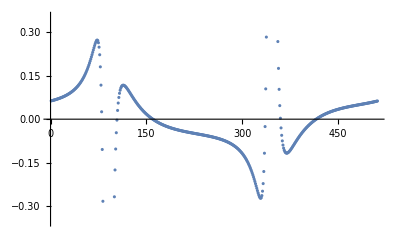

```mathematica
ListPlot[delpsic]
```

### Plot perturbations

```mathematica
Import["f.junk"]//Flatten;
```

```mathematica
nplot=(%//Length)/256
```

46

```mathematica
tgriddoub=Range[0,Delta,Delta/(2Nt)];
```

```mathematica
xvals=Import["xaxis.junk"]//Flatten;
```

```mathematica
Position[xvals,0.0998588027859638]
```

{{151}}

```mathematica
f=TakeList[Import["f.junk"]//Flatten,ConstantArray[256,nplot]];
u=TakeList[Import["u.junk"]//Flatten,ConstantArray[256,nplot]];
v=TakeList[Import["v.junk"]//Flatten,ConstantArray[256,nplot]];
```

```mathematica
ftab=Flatten[Table[{xvals[[i]],tgriddoub[[j]],f[[i,j]]},{i,1,nplot},{j,1,2Nt}],1];
utab=Flatten[Table[{xvals[[i]],tgriddoub[[j]],u[[i,j]]},{i,1,nplot},{j,1,2Nt}],1];
vtab=Flatten[Table[{xvals[[i]],tgriddoub[[j]],v[[i,j]]},{i,1,nplot},{j,1,2Nt}],1];
```

```mathematica
fpowertab=Flatten[Table[{xvals[[i]],j,Log10[Abs[1/(√(2Nt))Fourier[f[[i,;;]]][[j]]]]},{i,1,nplot},{j,1,Nt/2}],1];
upowertab=Flatten[Table[{xvals[[i]],j,Log10[Abs[1/(√(2Nt))Fourier[u[[i,;;]]][[j]]]]},{i,1,nplot},{j,1,Nt/2}],1];
vpowertab=Flatten[Table[{xvals[[i]],j,Log10[Abs[1/(√(2Nt))Fourier[v[[i,;;]]][[j]]]]},{i,1,nplot},{j,1,Nt/2}],1];
```

```mathematica
{ListPlot3D[fpowertab,ImageSize->350,PlotLabel->"fspec"],ListPlot3D[upowertab,ImageSize->350,PlotLabel->"uspec"],ListPlot3D[vpowertab,ImageSize->350,PlotLabel->"vspec"]}
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-}

```mathematica
ftabL=Flatten[Table[{xvals[[i]],tgriddoub[[j]],f[[i,j]]},{i,1,151,2},{j,1,2Nt}],1];
ftabR=Flatten[Table[{xvals[[i]],tgriddoub[[j]],f[[i,j]]},{i,152,nplot,2},{j,1,2Nt}],1];
utabL=Flatten[Table[{xvals[[i]],tgriddoub[[j]],u[[i,j]]},{i,1,151,2},{j,1,2Nt}],1];
utabR=Flatten[Table[{xvals[[i]],tgriddoub[[j]],u[[i,j]]},{i,152,nplot,2},{j,1,2Nt}],1];
vtabL=Flatten[Table[{xvals[[i]],tgriddoub[[j]],v[[i,j]]},{i,1,151,2},{j,1,2Nt}],1];
vtabR=Flatten[Table[{xvals[[i]],tgriddoub[[j]],v[[i,j]]},{i,152,nplot,2},{j,1,2Nt}],1];
```

Part::partw: Part 103 of {0.001,0.00109694,0.00120515,0.00132403,0.00145461,0.00159805,0.00175561,0.00192868,0.00211877,0.00232755,«91»} does not exist.

Part::partw: Part 103 of {{0.0000998031,0.000102098,0.000104469,0.00010692,0.000109449,0.000112055,0.000114743,0.000117516,0.000120372,0.000123311,«246»},{0.000099805,0.0001021,0.000104471,0.000106922,0.000109451,0.000112057,0.000114745,0.000117519,0.000120375,0.000123313,«246»},«7»,{0.0000998455,0.000102143,0.000104515,0.000106965,0.000109495,0.000112103,0.000114793,0.000117566,0.000120423,0.000123365,«246»},«91»} does not exist.

Part::partw: Part 103 of {0.001,0.00109694,0.00120515,0.00132403,0.00145461,0.00159805,0.00175561,0.00192868,0.00211877,0.00232755,«91»} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::partw: Part 103 of {0.001,0.00109694,0.00120515,0.00132403,0.00145461,0.00159805,0.00175561,0.00192868,0.00211877,0.00232755,«91»} does not exist.

Part::partw: Part 103 of {{0.0000145645,0.0000145278,0.0000145021,0.0000144562,0.0000144404,0.0000144878,0.0000145475,0.0000145864,0.0000146599,0.0000148045,«246»},{0.0000159699,0.0000159285,0.0000159002,0.0000158507,0.0000158332,0.0000158841,0.0000159494,0.0000159928,0.0000160734,0.0000162308,«246»},«7»,{0.0000337001,0.0000336006,0.0000335299,0.0000334298,0.000033396,0.0000334916,0.0000336188,0.0000337146,0.0000338872,0.0000342075,«246»},«91»} does not exist.

Part::partw: Part 103 of {0.001,0.00109694,0.00120515,0.00132403,0.00145461,0.00159805,0.00175561,0.00192868,0.00211877,0.00232755,«91»} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::partw: Part 103 of {0.001,0.00109694,0.00120515,0.00132403,0.00145461,0.00159805,0.00175561,0.00192868,0.00211877,0.00232755,«91»} does not exist.

Part::partw: Part 103 of {{0.0000146901,0.0000146597,0.0000146333,0.0000145858,0.0000145759,0.0000146305,0.0000146899,0.0000147276,0.0000148081,0.000014961,«246»},{0.00001612,0.0000160882,0.000016059,0.0000160057,0.0000159953,0.0000160567,0.0000161217,0.0000161618,0.0000162505,0.0000164199,«246»},«7»,{0.0000343759,0.0000343337,0.0000342436,0.0000341109,0.0000341239,0.0000342832,0.0000343948,0.0000344583,0.0000346814,0.0000350733,«246»},«91»} does not exist.

Part::partw: Part 103 of {0.001,0.00109694,0.00120515,0.00132403,0.00145461,0.00159805,0.00175561,0.00192868,0.00211877,0.00232755,«91»} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

```mathematica
ListPlot3D[ftab,PlotRange->All]
```

-Graphics3D-

```mathematica
ListPlot3D[vtab,PlotRange->All]
```

-Graphics3D-

```mathematica
ListPlot3D[{ftabL,ftabR},PlotRange->All]
```

-Graphics3D-

```mathematica
ListPlot3D[{utabL,utabR},PlotRange->All]
```

-Graphics3D-

```mathematica
ListPlot3D[{vtabL,vtabR},PlotRange->All]
```

-Graphics3D-

### Determinant

```mathematica
n3=3*Nt/2
```

192

```mathematica
doutdinraw=Import["doutdin.junk","List"]
```

```mathematica
doutdin=TakeList[doutdinraw,ConstantArray[n3+1,n3]][[;;,;;-2]]
```

```mathematica
doutdin//Dimensions
```

{192,192}

```mathematica
Det[doutdin*100]
```

Det::luc: Result for Det of badly conditioned matrix {{181.679,-130.477,-16.7578,-9.52663,1.77382,1.5622,-0.294904,-0.352741,0.0419459,0.0773914,«182»},{119.616,259.453,14.7298,-26.6201,-2.75778,3.66017,0.655959,-0.6193,-0.14936,0.0933726,«182»},«7»,{0.00298773,-0.0413633,-0.0283886,0.172011,0.581524,-0.73125,-19.3488,7.04899,-248.889,114.531,«182»},«182»} may contain significant numerical errors.

4.57987036541448×10^325

```mathematica
abse=Log10[Abs[Eigenvalues[doutdin*100]]]//Total
```

325.642

```mathematica
expon=%/n3
```

1.69605

```mathematica
Det[doutdin*100*10^-expon]
```

Det::luc: Result for Det of badly conditioned matrix {{3.65808,-2.62713,-0.337416,-0.191817,0.0357155,0.0314547,-0.00593784,-0.00710238,0.000844572,0.00155826,«182»},{2.40845,5.22404,0.296583,-0.535992,-0.0555275,0.073697,0.0132076,-0.0124695,-0.00300733,0.00188004,«182»},«8»,«182»} may contain significant numerical errors.

1.04428

```mathematica
2.674079-2.674078
```

1.×10^-6